```mathematica
$ProcessorCount
LaunchKernels[]
(*Needs["FourierSeries`"]*)
```

2

LaunchKernels::nodef: Some subkernels are already running. Not launching default kernels again.

$Failed

```mathematica
Needs["CCompilerDriver`GenericCCompiler`"]
(*$CCompiler={"Compiler"->GenericCCompiler,"CompilerInstallation"->"E:\\mingw-w64\\x86_64-8.1.0-posix-seh-rt_v6-rev0\\mingw64","CompilerName"->"x86_64-w64-mingw32-gcc.exe"};*)
$CCompiler={"Name"->"Visual Studio","Compiler"->CCompilerDriver`VisualStudioCompiler`VisualStudioCompiler,"CompilerInstallation"->"C:\\Program Files (x86)\\Microsoft Visual Studio\\2017\\Community","CompilerName"->Automatic};
<<CompiledFunctionTools`(*позволяет смотреть "код"*)
```

```mathematica
Nc=40;(*число периодов в холестерике*)
qc=1;(*волновой вектор холестерика в эВ*)
Lz=2 Pi/qc Nc ;(*толщина пластины холестерика в 1/эВ*)
lev=1.24;(*длина волны фотона энергии 1 эВ в мкм. lev/(2 Pi) -- единица длины*)
mMax =10;(*ожидаемое максимальное значение m*)
```

```mathematica
ϵpp=Compile[{{k0,_Real}},2.4,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*перпендикулярная диэлектрическая проницаемость*)
ϵpl=Compile[{{k0,_Real}},2.9,CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*параллельная диэлектрическая проницаемость*)
dec=Compile[{{k0,_Real}},(ϵpl[k0]-ϵpp[k0])/ϵpp[k0],CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*анизотропия*)
ϵvac=1(*1/2 (ϵpp[qc]+ϵpl[qc])*);(*диэлектрическая проницаемость окружающей среды*)
Print["Волновой вектор холестерика q: ",qc, " эВ"]
Print["Толщина пластины холестерика Lz: ",Lz lev/(2 Pi), " мкм"]
Module[{xx=83},(*предполагаемая энергия фотона*)
Print["Показатели преломления: n_perp=",Sqrt[ϵpp[xx]], ", n_parallel=",Sqrt[ϵpl[xx]],", n_vac=",Sqrt[ϵvac]];
Print["Анизотропия de: ",dec[xx]]]
```

Волновой вектор холестерика q: 1 эВ

Толщина пластины холестерика Lz: 49.6 мкм

Показатели преломления: n_perp=1.54919, n_parallel=1.70294, n_vac=1

Анизотропия de: 0.208333

```mathematica
(*risse2018: no=1.5; ne=1.8; nvac=1.4688*)
```

```mathematica
e3={0,0,1};
e1={1,0,0};
e2={0,1,0};
ep=e1+ⅈ e2;
em=e1-ⅈ e2;
```

```mathematica
pp=10;(*2p+1-волновое приближение*)
```

```mathematica
aaa[n_]:={{k0s-kp^2-(qn+2 n)^2+de (k0s-kp^2/2)/2,de (k0s-kp^2/2)/2},{de (k0s-kp^2/2)/2,k0s-kp^2-(qn+2 n-2)^2+de (k0s-kp^2/2)/2}};
bbb[n_]:=-kp^2 de/4 {{1,1},{0,0}};
ccc[n_]:=-kp^2 de/4 {{0,0},{1,1}};
```

```mathematica
mmi[p_]:=Module[{mm1,i},
mm1=ConstantArray[0,{2p+1,2p+1}];
Do[
mm1[[i,i]]=aaa[p-i+1];
If[i<2p+1,mm1[[i,i+1]]=ccc[p-i+1]];
If[i>1,mm1[[i,i-1]]=bbb[p-i+1]];
,{i,1,2 p+1}];
Drop[Drop[ArrayFlatten[mm1],-1,-1],1,1]]
```

```mathematica
If[FailureQ[FindFile[NotebookDirectory[]<>"DisperDet"<>ToString[pp]<>".dat"]]==True,
dspp=If[pp≤10,Collect[Det[mmi[pp]],qn,Simplify],
Collect[Det[mmi[pp]],qn]];(*дисперсионнный определитель. если есть, то загружается из файла*)
Put[dspp,NotebookDirectory[]<>"DisperDet"<>ToString[pp]<>".dat"];,
dspp=Get[NotebookDirectory[]<>"DisperDet"<>ToString[pp]<>".dat"];]

mmieq=mmi[pp];(*матрица уравнения*)
```

```mathematica
dsp[k0s1_?NumberQ,kp1_?NumberQ,de1_?NumberQ,qn1_]=dspp/.{k0s->k0s1,kp->kp1,de->de1,qn->qn1};
meq=Compile[{{k0s1,_Real},{kp1,_Real},{de1,_Real},{qn1,_Complex}},Evaluate[mmieq/.{k0s->k0s1,kp->kp1,de->de1,qn->qn1}],RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*функции для определителя и матрицы*)
```

```mathematica
PolynomialQ[dspp,qn]
```

True

```mathematica
ChoiceMainBranch=Compile[{{p,_Integer},{k0s,_Real},{kp,_Real},{de,_Real},{rts,_Complex,1}},Module[{i,j,k,nmax,ff,rtss,mm1,mm1n,eigv,eigv1,eigvr,partnorm,nv1,crit=0.5},
Do[
rtss=rts[[i]];
mm1n=meq[k0s,kp,de,rtss];
eigv=NullSpace[mm1n];
Do[
eigv1=eigv[[k]];
nv1=Norm[eigv[[k]]];
eigv1=eigv1/nv1;
partnorm=Abs[eigv1[[2 p]]]^2+Abs[eigv1[[2 p+1]]]^2+Abs[eigv1[[2 p-1]]]^2;(*+Abs[eigv1[[2 p-1]]]^2*)
If[partnorm<crit,,
eigvr=Append[eigv1,rtss];
Sow[eigvr];](*записываем в стек (СВ,СЗ), СЗ -- последний элемент с номером 4p+1*);
,{k,1,Length[eigv]}];
,{i,1,Length[rts]}];
],{{NullSpace[_],_Complex,2},{Length[_],_Integer},{Norm[_],_Real},{meq[_,_,_,_],_Complex,2},{Sow[_],_Complex,1}},RuntimeOptions->{"Speed"},CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"];

Branches[p_?NumberQ,k0s_?NumberQ,kp_?NumberQ,de_?NumberQ]:=Module[{rts,ddsp,q1,bb},
ddsp=dsp[k0s,kp,de,q1];
rts=q1/.{ToRules[NRoots[ddsp==0,q1,PrecisionGoal->30]]};
bb=Reap[ChoiceMainBranch[p,k0s,kp,de,rts]];
Last[bb][[1]]];
```

```mathematica
SetSharedFunction[ParallelSow]
ParallelSow[ex_]:=Sow[ex];
```

```mathematica
DisperMain[p_?IntegerQ,de1_?NumberQ,kp1_?NumberQ,k0i_?NumberQ,k0f_?NumberQ,dk0_?NumberQ]:=Module[{k0,k0ie,k0fe,dk0e,kpe,dee},
k0ie=SetPrecision[k0i,Infinity];
k0fe=SetPrecision[k0f,Infinity];
dk0e=SetPrecision[dk0,Infinity];
kpe=SetPrecision[kp1,Infinity];
dee=SetPrecision[de1,Infinity];(*точные числа*)
Last[Reap[
Parallelize[
Do[Module[{llb,i},
llb=Branches[p,k0^2,kpe,dee];
Do[ParallelSow[{llb[[i,4 p+1]],k0}],{i,1,Length[llb]}]]
,{k0,k0ie,k0fe,dk0e}]]]][[1]]];

With[{qc=qc},
DisperMainK00np[p_?IntegerQ,np1_?NumberQ,k0i_?NumberQ,k0f_?NumberQ,dk0_?NumberQ]:=Module[{k0,k0ie,k0fe,dk0e,npe},
k0ie=SetPrecision[k0i,Infinity];
k0fe=SetPrecision[k0f,Infinity];
dk0e=SetPrecision[dk0,Infinity];
npe=SetPrecision[np1,Infinity];(*точные числа*)

Last[Reap[
Parallelize[
Do[Module[{llb,i,k0s,dee,k00,kp},
k00=k0 qc;
k0s=SetPrecision[ϵpp[k00] k0^2,Infinity];
dee=SetPrecision[dec[k00],Infinity];
kp=k0 npe;
llb=Branches[p,k0s,kp,dee];
Do[ParallelSow[{llb[[i,4 p+1]],k0}],{i,1,Length[llb]}]]
,{k0,k0ie,k0fe,dk0e}]]]][[1]]];]
```

```mathematica
DisperSimpl[de1_?NumberQ,kp1_?NumberQ,k0i_?NumberQ,k0f_?NumberQ,dk0_?NumberQ]:=Module[{k0,k0ie,k0fe,dk0e,kpe,dee},
k0ie=SetPrecision[k0i,Infinity];
k0fe=SetPrecision[k0f,Infinity];
dk0e=SetPrecision[dk0,Infinity];
kpe=SetPrecision[kp1,Infinity];
dee=SetPrecision[de1,Infinity];(*точные числа*)
Last[Reap[
Parallelize[
Do[Module[{rts1,rts2,i,dssp,q1},
dssp=dsp[k0^2,kpe,dee,q1];
rts1=q1/.{ToRules[NRoots[dssp==0,q1,PrecisionGoal->30]]};
rts2=Sort[Select[rts1,(Chop[#]∈Reals)&]];(*оставляем только вещественные корни*)
Do[ParallelSow[{Re[rts2[[i]]],k0}],{i,1,Length[rts2]}]]
,{k0,k0ie,k0fe,dk0e}]]]][[1]]];
```

```mathematica
(*vvvvvvvv+аналитический расчёт блоков матриц, входящих в уравнения сшивки+vvvvvvvvv*)
```

```mathematica
h0l={{((-sϵvac+n3) t0l)/(√2),((sϵvac+n3) t0l)/(√2),(-sϵvac-n3)/(√2 t0l),(sϵvac-n3)/(√2 t0l)},{((sϵvac+n3) t0l)/(√2),((-sϵvac+n3) t0l)/(√2),(sϵvac-n3)/(√2 t0l),(-sϵvac-n3)/(√2 t0l)},{(k0 (ϵvac-sϵvac n3) t0l)/(√2),(k0 (ϵvac+sϵvac n3) t0l)/(√2),(k0 (ϵvac+sϵvac n3))/(√2 t0l),(k0 (ϵvac-sϵvac n3))/(√2 t0l)},{(k0 (ϵvac+sϵvac n3) t0l)/(√2),(k0 (ϵvac-sϵvac n3) t0l)/(√2),(k0 (ϵvac-sϵvac n3))/(√2 t0l),(k0 (ϵvac+sϵvac n3))/(√2 t0l)}};
Gm={{(n3-sϵvac)/(√2),(n3+sϵvac)/(√2)},{(n3+sϵvac)/(√2),(n3-sϵvac)/(√2)},{(k0 (ϵvac-sϵvac n3))/(√2),(k0 (ϵvac+sϵvac n3))/(√2)},{(k0 (sϵvac n3+ϵvac))/(√2),(k0 (-sϵvac n3+ϵvac))/(√2)}};
```

```mathematica
-PadRight[h0l[[All,3;;4]],{4,4}]
-PadLeft[Gm,{4,4}]
```

{{-(-n3-sϵvac)/(√2 t0l),-(-n3+sϵvac)/(√2 t0l),0,0},{-(-n3+sϵvac)/(√2 t0l),-(-n3-sϵvac)/(√2 t0l),0,0},{-(k0 (1+n3 sϵvac))/(√2 t0l),-(k0 (1-n3 sϵvac))/(√2 t0l),0,0},{-(k0 (1-n3 sϵvac))/(√2 t0l),-(k0 (1+n3 sϵvac))/(√2 t0l),0,0}}

{{0,0,-(n3-sϵvac)/(√2),-(n3+sϵvac)/(√2)},{0,0,-(n3+sϵvac)/(√2),-(n3-sϵvac)/(√2)},{0,0,-(k0 (1-n3 sϵvac))/(√2),-(k0 (1+n3 sϵvac))/(√2)},{0,0,-(k0 (1+n3 sϵvac))/(√2),-(k0 (1-n3 sϵvac))/(√2)}}

```mathematica
h0l[[All,1;;2]]
h0l[[All,1;;2]].{dp,dm}//FullSimplify
```

{{((n3-sϵvac) t0l)/(√2),((n3+sϵvac) t0l)/(√2)},{((n3+sϵvac) t0l)/(√2),((n3-sϵvac) t0l)/(√2)},{(k0 (1-n3 sϵvac) t0l)/(√2),(k0 (1+n3 sϵvac) t0l)/(√2)},{(k0 (1+n3 sϵvac) t0l)/(√2),(k0 (1-n3 sϵvac) t0l)/(√2)}}

{((dp (n3-sϵvac)+dm (n3+sϵvac)) t0l)/(√2),((dm (n3-sϵvac)+dp (n3+sϵvac)) t0l)/(√2),(k0 (dm+dp+(dm-dp) n3 sϵvac) t0l)/(√2),(k0 (dm+dp-dm n3 sϵvac+dp n3 sϵvac) t0l)/(√2)}

```mathematica
(*^^^^^^^^^^+аналитический расчёт блоков матриц, входящих в уравнения сшивки+^^^^^^^^^^^*)
```

```mathematica
ClearAll[ScCoeffLinComb]
```

```mathematica
With[{qc=qc,Lz=Lz,ϵvac=ϵvac,sϵvac=Evaluate[Sqrt[ϵvac]]},
ScCoeffLinComb=Compile[{{dp,_Complex},{dm,_Complex},{k00,_Real},{k0,_Real},{kp,_Real},{npx,_Real},{npy,_Real},{n3,_Real},{k3b,_Real},{p,_Integer},{branchs,_Complex,2},{numb,_Integer}},Module[{ii,r,ϕ,rff,u0t,umLt,t0l,h0l20,Gm0,frterm,row1,row2,eqnmb,brt},

ϕ=Arg[npx+I npy];rff=Exp[I ϕ];
r=1/rff^2;(*общие фазовые множители*)

u0t=Table[Module[{tf,pf,ap,am,mrap,ram,l},(*транспонированная матрица U(0)*)
pf=branchs[[ii,4 p+1]];(*импульс закона дисперсии*)
tf=Exp[-I pf ϕ];(*фазовые множители, зависящие от ветви*)
ap=0.+I 0.;
am=0.+I 0.;
mrap=0.+I 0.;
ram=0.+I 0.;
Do[Module[{apl,aml},
apl=branchs[[ii,2 l]];
aml=branchs[[ii,2 l-1]];
ap+=r^(p-l) apl;
am+=r^(p-l) aml;
mrap+=r^(p-l) (apl+kp^2/(2 k3b^2) (apl+aml)) (pf+2 (p-l));
ram+=r^(p-l) (aml+kp^2/(2 k3b^2) (apl+aml)) (pf+2 (p-l));]
,{l,1,2 p}];
{tf ap,tf am,tf mrap,tf ram}]
,{ii,1,numb}];

umLt=Table[Module[{tfl},(*транспонированная матрица U(-L). предполагаем целое число периодов*)
tfl=Exp[-I branchs[[ii,4 p+1]] qc Lz];
tfl u0t[[ii]]]
,{ii,1,numb}];

t0l=Exp[-I k00 n3 Lz];

h0l20={{-(-n3-sϵvac)/(√2 t0l),-(-n3+sϵvac)/(√2 t0l),0,0},{-(-n3+sϵvac)/(√2 t0l),-(-n3-sϵvac)/(√2 t0l),0,0},{-(k0 (n3 sϵvac+ϵvac))/(√2 t0l),-(k0 (-n3 sϵvac+ϵvac))/(√2 t0l),0,0},{-(k0 (-n3 sϵvac+ϵvac))/(√2 t0l),-(k0 (n3 sϵvac+ϵvac))/(√2 t0l),0,0}};
Gm0={{0,0,-(n3-sϵvac)/(√2),-(n3+sϵvac)/(√2)},{0,0,-(n3+sϵvac)/(√2),-(n3-sϵvac)/(√2)},{0,0,-(k0 (-n3 sϵvac+ϵvac))/(√2),-(k0 (n3 sϵvac+ϵvac))/(√2)},{0,0,-(k0 (n3 sϵvac+ϵvac))/(√2),-(k0 (-n3 sϵvac+ϵvac))/(√2)}};

frterm={((dp (n3-sϵvac)+dm (n3+sϵvac)) t0l)/(√2),((dm (n3-sϵvac)+dp (n3+sϵvac)) t0l)/(√2),(k0 t0l ((dm-dp) n3 sϵvac+(dm+dp) ϵvac))/(√2),(k0 t0l (dm (-n3 sϵvac+ϵvac)+dp (n3 sϵvac+ϵvac)))/(√2),0,0,0,0};

row1=Join[Transpose[umLt],h0l20,2];
row2=Join[Transpose[u0t],Gm0,2];
eqnmb=Join[row1,row2];(*блочная матрица уравнения*)

brt=LinearSolve[eqnmb,frterm];

brt[[numb+1;;numb+4]]

],{{LinearSolve[_,_],_Complex,1}},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationOptions->{"InlineExternalDefinitions"->True,"ExpressionOptimization"->True},CompilationTarget->"C"]];
(*выдает ответ в виде списка (hp,hm,tp,tm). При желании можно выводить и ach.*)
```

```mathematica
With[{qc=qc,ϵvac=ϵvac},
ScAmplitPlane[ip_?NumberQ,im_?NumberQ,k001_?NumberQ,npx1_?NumberQ,npy1_?NumberQ,p_?IntegerQ]:=Module[{npx,npy,k00,k0,k0s,np,n3,kp,k3b,de,branchs,numb},

npx=N[npx1];(*часто используемые постоянные*)
npy=N[npy1];
k00=N[k001];

k0=k00/qc;
k0s=SetPrecision[ϵpp[k00] k0^2,Infinity];
np=Sqrt[npx^2+npy^2];
n3=N[Sqrt[ϵvac-np^2]];
kp=SetPrecision[k0 np,Infinity];
k3b=N[Sqrt[k0s-kp^2]];
de=SetPrecision[dec[k00],Infinity];

branchs=Branches[p,k0s,kp,de];(*находим импульсы и им соответствующие ветви*)
numb=Length[branchs];(*число ветвей*)

ScCoeffLinComb[ip,im,k00,k0,kp,npx,npy,n3,k3b,p,branchs,numb]


]](*амплитуда перехода. выдает {rp,rm,tp,tm}*)
```

```mathematica
(*^^^^^^^^^^^^-конец плосковолнового кода-^^^^^^^^^^*)
```

```mathematica
ClearAll[ScAmplTwistTab,ScAmplTwist]
```

```mathematica
(*vvvvvvvvvv-закрученные фотоны-vvvvvvvvvvvvvvvvvvvv*)
```

```mathematica
With[{qc=qc,mMax=mMax,ϵvac=ϵvac},
ScAmplTwistTab[ip_?NumberQ,im_?NumberQ,m_?IntegerQ,k00_?NumberQ,kpp_?NumberQ,p_?IntegerQ]:=Module[{Npt,np,amplPlTab,amplTwTab,k0,k0s,kp,n3,k3b,de,branchs,numb,n1,ii},
np=N[kpp/k00];
k0=N[k00/qc]; (*часто используемые величины*)
k0s=SetPrecision[ϵpp[k00] k0^2,Infinity];
n3=N[Sqrt[ϵvac-np^2]];
kp=SetPrecision[k0 np,Infinity];
k3b=N[Sqrt[k0s-kp^2]];
de=SetPrecision[dec[k00],Infinity];

Npt=2^(Floor[Log[2,20 mMax]]);(*число элементов таблицы*)

branchs=Branches[p,k0s,kp,de];(*находим импульсы и им соответствующие ветви*)
numb=Length[branchs];(*число ветвей*)

amplPlTab=ParallelTable[Module[{npx,npy,ϕ,csf,scf,emf},
ϕ=N[2 Pi (n1-1)/Npt];
csf=Cos[ϕ];
scf=Sin[ϕ];
emf=(csf+I scf)^m;
npx=np csf;npy=np  scf;emf ScCoeffLinComb[ip,im,k00,k0,kp,npx,npy,n3,k3b,p,branchs,numb]],{n1,1,Npt}];(*таблица значений плосковолновой амплитуды*)

amplTwTab=I^(-m) ParallelTable[
Chop[Fourier[amplPlTab[[All,ii]],FourierParameters->{-1,-1}]],{ii,1,4}];(*таблица значений закрученной амплитуды с m=s-1 и m+Npt=m. b=-1 дает к.с. ответ*)

{Npt,amplPlTab,amplTwTab}]](*на выходе: {число элементов, табл1, табл2}*)
```

```mathematica
ScAmplTwist=Compile[{{mm,_Integer},{num,_Integer},{amplli,_Complex,2}},Module[{Npt=Length[amplli[[1]]]},
I^(mm)amplli[[num,1+Mod[mm,Npt]]]],CompilationOptions->{"ExpressionOptimization"->True},RuntimeOptions->{"Speed","EvaluateSymbolically"->False},CompilationTarget->"C"];(*амплитуда с правильной фазой *)
```

```mathematica
(*нужно сначала вызвать ll=ScAmplTwistTab[ip,im,m,k00,kpp,pp], а потом ScAmplTwist[m,num,ll[[3]]] для нужного значения m; num=1-4, соответствует {rp,rm,tp,tm} для заданного значения m*)
```

```mathematica
(*^^^^^^^^^^^-конец кода для закрученных фотонов-^^^^^^^^^^^^^^^^^*)
```

```mathematica
(*vvvvv-примеры-vvvvvv*)
```

```mathematica
(*vvvvv-плоские фотоны-vvvvvv*)
```

```mathematica
ScAmplitPlane[ip,im,k001,npx1,npy1,p]
```

```mathematica
ScAmplitPlane[1,0,10,0,0,pp]//Norm
```

1.

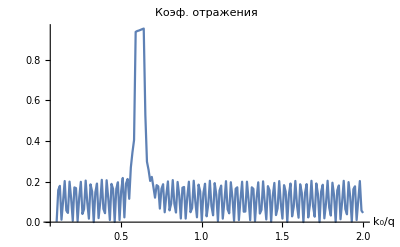

```mathematica
k0min=0.1;
k0max=2;
k0step=0.01;
calc=ParallelTable[{k0,ScAmplitPlane[0,1,k0,0,0,pp]},{k0,k0min,k0max,k0step}];
tp=ParallelTable[{calc[[i]][[1]],Abs[calc[[i]][[2]][[1]]]^2+Abs[calc[[i]][[2]][[2]]]^2},{i,1,1+(k0max-k0min)/k0step}];
ListLinePlot[tp,PlotRange->All,AxesLabel-> {"k_0/q",None},PlotLabel->"Коэф. отражения"]
```

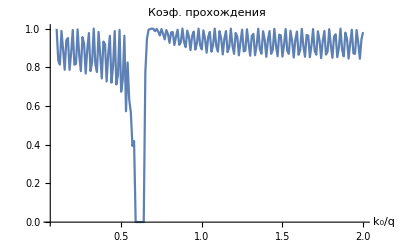

```mathematica
k0min=0.1;
k0max=2;
k0step=0.01;
calc=ParallelTable[{k0,ScAmplitPlane[0,1,k0,0,0,pp]},{k0,k0min,k0max,k0step}];
tp=ParallelTable[{calc[[i]][[1]],Abs[calc[[i]][[2]][[3]]]^2+Abs[calc[[i]][[2]][[4]]]^2},{i,1,1+(k0max-k0min)/k0step}];
ListLinePlot[tp,PlotRange->All,AxesLabel-> {"k_0/q",None},PlotLabel->"Коэф. прохождения"]
```

```mathematica
D[y[x]/x,x]
```

-y[x]/x^2+y'[x]/x

```mathematica
Branches[pp,2.4,0,0.2]
```

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.999739+0. ⅈ,0.0228263+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.62649+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.0957947+0. ⅈ,0.995401+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-1.61768+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.0957947+0. ⅈ,0.995401+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.382316+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.995401+0. ⅈ,0.0957947+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.61768+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.0228263+0. ⅈ,0.999739+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,1.62649+0. ⅈ}}

```mathematica
ScAmplitPlane[1,0,1,0,0,pp]
```

{0.0532992-0.0221504 ⅈ,-0.000711879+0.00421917 ⅈ,0.378621+0.921957 ⅈ,0.000707049+0.0573736 ⅈ}

```mathematica
ScAmplitPlane[1,0,10,1/10,1/10,10];//RepeatedTiming
```

{1.67,Null}

```mathematica
ScAmplitPlane[1,0,3,1/5,1/10,10]
```

$Aborted

```mathematica
Norm[ScAmplitPlane[1,0,3,1/5,1/10,10]]
```

1.

```mathematica
lk01=Module[{k0,k0i=1/100,k0f=5,dk0=1/10,np=1/50,tt},tt=ParallelTable[{k0,ScAmplitPlane[1,0,k0,np,0,pp]},{k0,k0i,k0f,dk0}]];
```

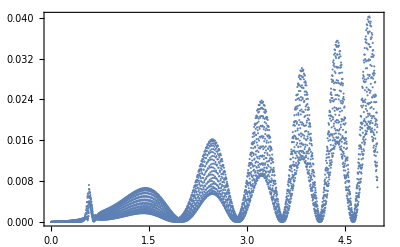
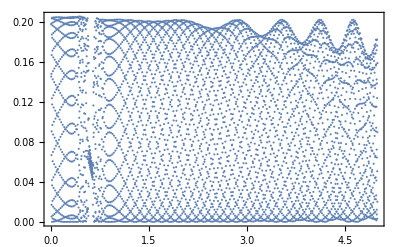
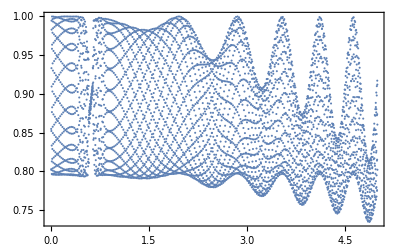
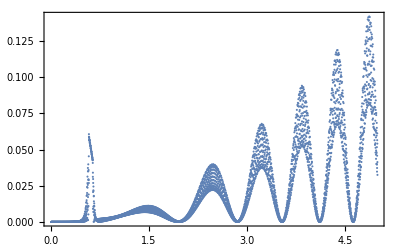

```mathematica
Module[{ii},Table[ListPlot[Join[Transpose[{lk01[[All,1]]}],Transpose[{Abs[lk01[[All,2]][[All,ii]]]^2}],2],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
lk02=Module[{k0,k0i=1/100,k0f=5,dk0=1/10,np=1/50,tt},tt=ParallelTable[{k0,ScAmplitPlane[0,1,k0,np,0,pp]},{k0,k0i,k0f,dk0}]];
```

$Aborted

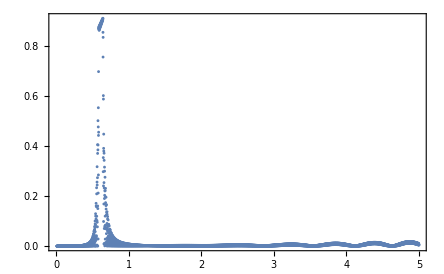
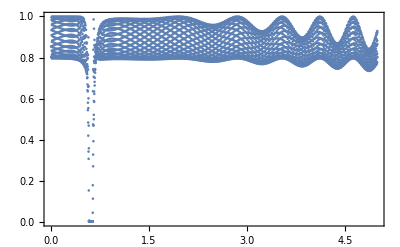
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{ii},Table[ListPlot[Join[Transpose[{lk02[[All,1]]}],Transpose[{Abs[lk02[[All,2]][[All,ii]]]^2}],2],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
1/Sqrt[ϵpp[1]]
1/Sqrt[ϵpl[1]]
```

0.645497

0.58722

```mathematica
(*vvvvvvvv+np=1/5+vvvvvvvv*)
```

```mathematica
ll3d4=Module[{k0i=SetPrecision[0.6188,Infinity],k0f=SetPrecision[0.619,Infinity],dk0=1/100000,np=SetPrecision[1/5,Infinity]},Sort[DisperMainK00np[pp,np,k0i,k0f,dk0],#1[[2]]<#2[[2]]&]];
```

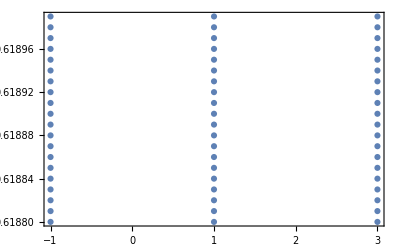

```mathematica
ListPlot[ll3d4,PlotRange->Full,Frame->True]
```

```mathematica
Chop[N[Select[ll3d4,(Re[#[[1]]]>0.9999&&Re[#[[1]]]<1.0001&&Chop[#[[1]]]∈Reals)&]]]
```

{{0.999911,0.61883},{0.999928,0.61884},{0.999944,0.61885},{0.99996,0.61886},{0.999976,0.61887},{0.999993,0.61888},{1.00001,0.61889},{1.00002,0.6189},{1.00004,0.61891},{1.00006,0.61892},{1.00007,0.61893},{1.00009,0.61894}}

```mathematica
Chop[N[Select[ll3d4,(Re[#[[2]]]>0.5915&&Re[#[[2]]]<0.5940&&Chop[#[[1]]]∈Reals)&]]]
```

{{2.95579,0.59155},{1.0054,0.59155},{0.994595,0.59155},{0.95579,0.59155},{-0.95579,0.59155},{-0.994595,0.59155},{2.95587,0.5916},{1.00464,0.5916},{0.995363,0.5916},{0.955871,0.5916},{-0.955871,0.5916},{-0.995363,0.5916},{2.95595,0.59165},{1.00372,0.59165},{0.996285,0.59165},{0.955952,0.59165},{-0.955952,0.59165},{-0.996285,0.59165},{2.95603,0.5917},{1.00247,0.5917},{0.997526,0.5917},{0.956033,0.5917},{-0.956033,0.5917},{-0.997526,0.5917},{2.95611,0.59175},{0.956113,0.59175},{-0.956113,0.59175},{2.95619,0.5918},{0.956194,0.5918},{-0.956194,0.5918},{2.95628,0.59185},{0.956275,0.59185},{-0.956275,0.59185},{2.95636,0.5919},{0.956356,0.5919},{-0.956356,0.5919},{2.95644,0.59195},{0.956437,0.59195},{-0.956437,0.59195},{2.95652,0.592},{0.956518,0.592},{-0.956518,0.592},{2.9566,0.59205},{0.956599,0.59205},{-0.956599,0.59205},{2.95668,0.5921},{0.95668,0.5921},{-0.95668,0.5921},{2.95676,0.59215},{0.95676,0.59215},{-0.95676,0.59215},{2.95684,0.5922},{0.956841,0.5922},{-0.956841,0.5922},{2.95692,0.59225},{0.956922,0.59225},{-0.956922,0.59225},{2.957,0.5923},{0.957003,0.5923},{-0.957003,0.5923},{2.95708,0.59235},{0.957084,0.59235},{-0.957084,0.59235},{2.95716,0.5924},{0.957165,0.5924},{-0.957165,0.5924},{2.95725,0.59245},{0.957246,0.59245},{-0.957246,0.59245},{2.95733,0.5925},{0.957326,0.5925},{-0.957326,0.5925},{2.95741,0.59255},{0.957407,0.59255},{-0.957407,0.59255},{2.95749,0.5926},{0.957488,0.5926},{-0.957488,0.5926},{2.95757,0.59265},{0.957569,0.59265},{-0.957569,0.59265},{2.95765,0.5927},{0.95765,0.5927},{-0.95765,0.5927},{2.95773,0.59275},{0.957731,0.59275},{-0.957731,0.59275},{2.95781,0.5928},{0.957812,0.5928},{-0.957812,0.5928},{2.95789,0.59285},{0.957893,0.59285},{-0.957893,0.59285},{2.95797,0.5929},{0.957973,0.5929},{-0.957973,0.5929},{2.95805,0.59295},{0.958054,0.59295},{-0.958054,0.59295},{2.95814,0.593},{0.958135,0.593},{-0.958135,0.593},{2.95822,0.59305},{0.958216,0.59305},{-0.958216,0.59305},{2.9583,0.5931},{0.958297,0.5931},{-0.958297,0.5931},{2.95838,0.59315},{0.958378,0.59315},{-0.958378,0.59315},{2.95846,0.5932},{0.958459,0.5932},{-0.958459,0.5932},{2.95854,0.59325},{0.958539,0.59325},{-0.958539,0.59325},{2.95862,0.5933},{0.95862,0.5933},{-0.95862,0.5933},{2.9587,0.59335},{0.958701,0.59335},{-0.958701,0.59335},{2.95878,0.5934},{0.958782,0.5934},{-0.958782,0.5934},{2.95886,0.59345},{0.958863,0.59345},{-0.958863,0.59345},{2.95894,0.5935},{0.958944,0.5935},{-0.958944,0.5935},{2.95902,0.59355},{0.959025,0.59355},{-0.959025,0.59355},{2.95911,0.5936},{0.959105,0.5936},{-0.959105,0.5936},{2.95919,0.59365},{0.959186,0.59365},{-0.959186,0.59365},{2.95927,0.5937},{0.959267,0.5937},{-0.959267,0.5937},{2.95935,0.59375},{0.959348,0.59375},{-0.959348,0.59375},{2.95943,0.5938},{0.959429,0.5938},{-0.959429,0.5938},{2.95951,0.59385},{0.95951,0.59385},{-0.95951,0.59385},{2.95959,0.5939},{0.959591,0.5939},{-0.959591,0.5939},{2.95967,0.59395},{0.959672,0.59395},{-0.959672,0.59395}}

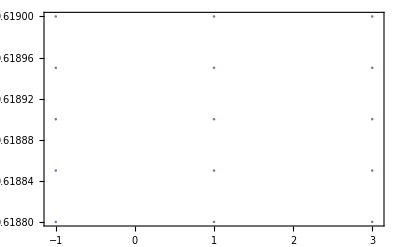

```mathematica
ListPlot[ll3d4,PlotRange->{0.6188,0.619},Frame->True]
```

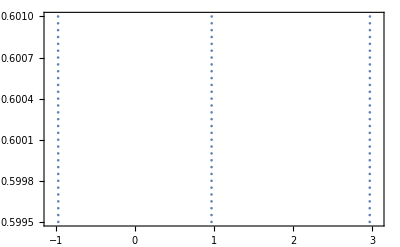

```mathematica
ListPlot[ll3d4,PlotRange->{0.5995,0.601},Frame->True]
```

```mathematica
(*^^^^^^^^^^+np=1/5+^^^^^^^^^^*)
```

```mathematica
(*vvvvvvvvvv-ищем полную щель-vvvvvvvvvv*)
```

```mathematica
ll3d=Module[{k0i=1/100,k0f=5,dk0=1/20,np=SetPrecision[0.8,Infinity]},Sort[DisperMainK00np[pp,np,k0i,k0f,dk0],#1[[2]]<#2[[2]]&]];
```

```mathematica
ll3d=Module[{k0i=1/100,k0f=5,dk0=1/20,np=SetPrecision[0.6,Infinity]},Sort[DisperMainK00np[pp,np,k0i,k0f,dk0],#1[[2]]<#2[[2]]&]];
```

```mathematica
ll3d1=Module[{k0i=1/100,k0f=5,dk0=1/100,np=SetPrecision[0.99,Infinity]},Sort[DisperMainK00np[pp,np,k0i,k0f,dk0],#1[[2]]<#2[[2]]&]];
```

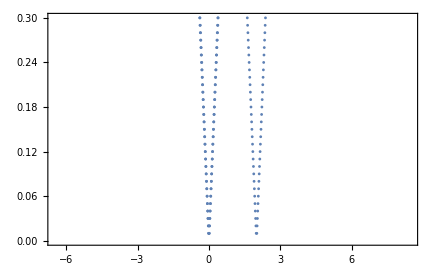
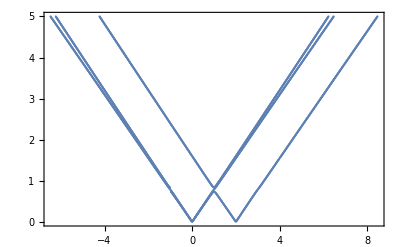

```mathematica
{ListPlot[ll3d1,PlotRange->{0,0.3},Frame->True],ListPlot[ll3d1,PlotRange->Full,Frame->True]}
```

```mathematica
ll3d2=Module[{k0i=6/10,k0f=1,dk0=1/1000,np=SetPrecision[0.99,Infinity]},Sort[DisperMainK00np[pp,np,k0i,k0f,dk0],#1[[2]]<#2[[2]]&]];
```

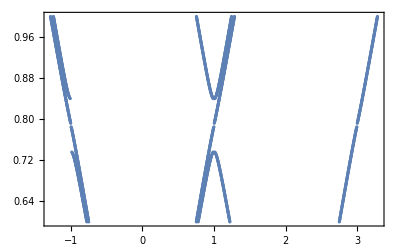

```mathematica
ListPlot[ll3d2,PlotRange->Full,Frame->True]
```

```mathematica
ll3d3=Module[{k0i=72/100,k0f=86/100,dk0=1/10000,np=SetPrecision[0.99,Infinity]},Sort[DisperMainK00np[pp,np,k0i,k0f,dk0],#1[[2]]<#2[[2]]&]];
```

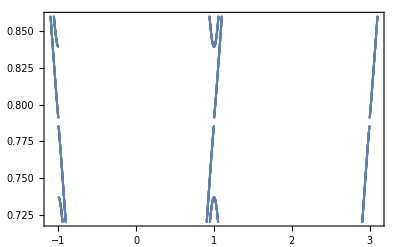

```mathematica
ListPlot[ll3d3,PlotRange->Full,Frame->True]
```

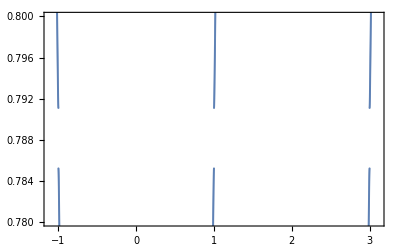

```mathematica
ListPlot[ll3d3,PlotRange->{0.78,0.8},Frame->True]
```

```mathematica
Chop[N[Select[ll3d3,(#[[2]]>0.785&&#[[2]]<0.791)&]]]
```

{{2.99881,0.7851},{1.+0.0569491 ⅈ,0.7851},{1.-0.0569491 ⅈ,0.7851},{0.998813,0.7851},{-0.998813,0.7851},{2.99961,0.7852},{1.+0.0569525 ⅈ,0.7852},{1.-0.0569525 ⅈ,0.7852},{0.999609,0.7852},{-0.999609,0.7852},{1.+0.0569557 ⅈ,0.7853},{1.-0.0569557 ⅈ,0.7853},{1.+0.0010308 ⅈ,0.7853},{1.-0.0010308 ⅈ,0.7853},{1.+0.00149539 ⅈ,0.7854},{1.-0.00149539 ⅈ,0.7854},{1.+0.0569587 ⅈ,0.7854},{1.-0.0569587 ⅈ,0.7854},{1.+0.00183526 ⅈ,0.7855},{1.-0.00183526 ⅈ,0.7855},{1.+0.0569615 ⅈ,0.7855},{1.-0.0569615 ⅈ,0.7855},{1.+0.0569641 ⅈ,0.7856},{1.-0.0569641 ⅈ,0.7856},{1.+0.00211151 ⅈ,0.7856},{1.-0.00211151 ⅈ,0.7856},{1.+0.0569666 ⅈ,0.7857},{1.-0.0569666 ⅈ,0.7857},{1.+0.00234672 ⅈ,0.7857},{1.-0.00234672 ⅈ,0.7857},{1.+0.00255226 ⅈ,0.7858},{1.-0.00255226 ⅈ,0.7858},{1.+0.0569688 ⅈ,0.7858},{1.-0.0569688 ⅈ,0.7858},{1.+0.0569708 ⅈ,0.7859},{1.-0.0569708 ⅈ,0.7859},{1.+0.00273481 ⅈ,0.7859},{1.-0.00273481 ⅈ,0.7859},{1.+0.0569726 ⅈ,0.786},{1.-0.0569726 ⅈ,0.786},{1.+0.00289874 ⅈ,0.786},{1.-0.00289874 ⅈ,0.786},{1.+0.00304703 ⅈ,0.7861},{1.-0.00304703 ⅈ,0.7861},{1.+0.0569742 ⅈ,0.7861},{1.-0.0569742 ⅈ,0.7861},{1.+0.0569756 ⅈ,0.7862},{1.-0.0569756 ⅈ,0.7862},{1.+0.00318188 ⅈ,0.7862},{1.-0.00318188 ⅈ,0.7862},{1.+0.00330493 ⅈ,0.7863},{1.-0.00330493 ⅈ,0.7863},{1.+0.0569768 ⅈ,0.7863},{1.-0.0569768 ⅈ,0.7863},{1.+0.0569778 ⅈ,0.7864},{1.-0.0569778 ⅈ,0.7864},{1.+0.00341746 ⅈ,0.7864},{1.-0.00341746 ⅈ,0.7864},{1.+0.0569787 ⅈ,0.7865},{1.-0.0569787 ⅈ,0.7865},{1.+0.00352046 ⅈ,0.7865},{1.-0.00352046 ⅈ,0.7865},{1.+0.00361475 ⅈ,0.7866},{1.-0.00361475 ⅈ,0.7866},{1.+0.0569793 ⅈ,0.7866},{1.-0.0569793 ⅈ,0.7866},{1.+0.0569797 ⅈ,0.7867},{1.-0.0569797 ⅈ,0.7867},{1.+0.00370101 ⅈ,0.7867},{1.-0.00370101 ⅈ,0.7867},{1.+0.0569799 ⅈ,0.7868},{1.-0.0569799 ⅈ,0.7868},{1.+0.00377976 ⅈ,0.7868},{1.-0.00377976 ⅈ,0.7868},{1.+0.00385148 ⅈ,0.7869},{1.-0.00385148 ⅈ,0.7869},{1.+0.0569799 ⅈ,0.7869},{1.-0.0569799 ⅈ,0.7869},{1.+0.0569797 ⅈ,0.787},{1.-0.0569797 ⅈ,0.787},{1.+0.00391655 ⅈ,0.787},{1.-0.00391655 ⅈ,0.787},{1.+0.0569793 ⅈ,0.7871},{1.-0.0569793 ⅈ,0.7871},{1.+0.00397529 ⅈ,0.7871},{1.-0.00397529 ⅈ,0.7871},{1.+0.00402798 ⅈ,0.7872},{1.-0.00402798 ⅈ,0.7872},{1.+0.0569788 ⅈ,0.7872},{1.-0.0569788 ⅈ,0.7872},{1.+0.056978 ⅈ,0.7873},{1.-0.056978 ⅈ,0.7873},{1.+0.00407485 ⅈ,0.7873},{1.-0.00407485 ⅈ,0.7873},{1.+0.056977 ⅈ,0.7874},{1.-0.056977 ⅈ,0.7874},{1.+0.0041161 ⅈ,0.7874},{1.-0.0041161 ⅈ,0.7874},{1.+0.0569758 ⅈ,0.7875},{1.-0.0569758 ⅈ,0.7875},{1.+0.0041519 ⅈ,0.7875},{1.-0.0041519 ⅈ,0.7875},{1.+0.0569744 ⅈ,0.7876},{1.-0.0569744 ⅈ,0.7876},{1.+0.00418238 ⅈ,0.7876},{1.-0.00418238 ⅈ,0.7876},{1.+0.0569729 ⅈ,0.7877},{1.-0.0569729 ⅈ,0.7877},{1.+0.00420766 ⅈ,0.7877},{1.-0.00420766 ⅈ,0.7877},{1.+0.0569711 ⅈ,0.7878},{1.-0.0569711 ⅈ,0.7878},{1.+0.00422783 ⅈ,0.7878},{1.-0.00422783 ⅈ,0.7878},{1.+0.0569691 ⅈ,0.7879},{1.-0.0569691 ⅈ,0.7879},{1.+0.00424296 ⅈ,0.7879},{1.-0.00424296 ⅈ,0.7879},{1.+0.00425311 ⅈ,0.788},{1.-0.00425311 ⅈ,0.788},{1.+0.056967 ⅈ,0.788},{1.-0.056967 ⅈ,0.788},{1.+0.0042583 ⅈ,0.7881},{1.-0.0042583 ⅈ,0.7881},{1.+0.0569646 ⅈ,0.7881},{1.-0.0569646 ⅈ,0.7881},{1.+0.00425856 ⅈ,0.7882},{1.-0.00425856 ⅈ,0.7882},{1.+0.056962 ⅈ,0.7882},{1.-0.056962 ⅈ,0.7882},{1.+0.0569593 ⅈ,0.7883},{1.-0.0569593 ⅈ,0.7883},{1.+0.00425389 ⅈ,0.7883},{1.-0.00425389 ⅈ,0.7883},{1.+0.0569563 ⅈ,0.7884},{1.-0.0569563 ⅈ,0.7884},{1.+0.00424426 ⅈ,0.7884},{1.-0.00424426 ⅈ,0.7884},{1.+0.00422965 ⅈ,0.7885},{1.-0.00422965 ⅈ,0.7885},{1.+0.0569531 ⅈ,0.7885},{1.-0.0569531 ⅈ,0.7885},{1.+0.0569498 ⅈ,0.7886},{1.-0.0569498 ⅈ,0.7886},{1.+0.00420999 ⅈ,0.7886},{1.-0.00420999 ⅈ,0.7886},{1.+0.0569462 ⅈ,0.7887},{1.-0.0569462 ⅈ,0.7887},{1.+0.00418523 ⅈ,0.7887},{1.-0.00418523 ⅈ,0.7887},{1.+0.0569425 ⅈ,0.7888},{1.-0.0569425 ⅈ,0.7888},{1.+0.00415526 ⅈ,0.7888},{1.-0.00415526 ⅈ,0.7888},{1.+0.0569385 ⅈ,0.7889},{1.-0.0569385 ⅈ,0.7889},{1.+0.00411997 ⅈ,0.7889},{1.-0.00411997 ⅈ,0.7889},{1.+0.0569344 ⅈ,0.789},{1.-0.0569344 ⅈ,0.789},{1.+0.00407922 ⅈ,0.789},{1.-0.00407922 ⅈ,0.789},{1.+0.00403284 ⅈ,0.7891},{1.-0.00403284 ⅈ,0.7891},{1.+0.05693 ⅈ,0.7891},{1.-0.05693 ⅈ,0.7891},{1.+0.0569255 ⅈ,0.7892},{1.-0.0569255 ⅈ,0.7892},{1.+0.00398065 ⅈ,0.7892},{1.-0.00398065 ⅈ,0.7892},{1.+0.0569208 ⅈ,0.7893},{1.-0.0569208 ⅈ,0.7893},{1.+0.00392239 ⅈ,0.7893},{1.-0.00392239 ⅈ,0.7893},{1.+0.00385781 ⅈ,0.7894},{1.-0.00385781 ⅈ,0.7894},{1.+0.0569158 ⅈ,0.7894},{1.-0.0569158 ⅈ,0.7894},{1.+0.00378657 ⅈ,0.7895},{1.-0.00378657 ⅈ,0.7895},{1.+0.0569107 ⅈ,0.7895},{1.-0.0569107 ⅈ,0.7895},{1.+0.00370828 ⅈ,0.7896},{1.-0.00370828 ⅈ,0.7896},{1.+0.0569053 ⅈ,0.7896},{1.-0.0569053 ⅈ,0.7896},{1.+0.0568998 ⅈ,0.7897},{1.-0.0568998 ⅈ,0.7897},{1.+0.0036225 ⅈ,0.7897},{1.-0.0036225 ⅈ,0.7897},{1.+0.00352867 ⅈ,0.7898},{1.-0.00352867 ⅈ,0.7898},{1.+0.0568941 ⅈ,0.7898},{1.-0.0568941 ⅈ,0.7898},{1.+0.00342613 ⅈ,0.7899},{1.-0.00342613 ⅈ,0.7899},{1.+0.0568882 ⅈ,0.7899},{1.-0.0568882 ⅈ,0.7899},{1.+0.056882 ⅈ,0.79},{1.-0.056882 ⅈ,0.79},{1.+0.00331407 ⅈ,0.79},{1.-0.00331407 ⅈ,0.79},{1.+0.0568757 ⅈ,0.7901},{1.-0.0568757 ⅈ,0.7901},{1.+0.00319149 ⅈ,0.7901},{1.-0.00319149 ⅈ,0.7901},{1.+0.0568692 ⅈ,0.7902},{1.-0.0568692 ⅈ,0.7902},{1.+0.00305712 ⅈ,0.7902},{1.-0.00305712 ⅈ,0.7902},{1.+0.00290933 ⅈ,0.7903},{1.-0.00290933 ⅈ,0.7903},{1.+0.0568625 ⅈ,0.7903},{1.-0.0568625 ⅈ,0.7903},{1.+0.00274595 ⅈ,0.7904},{1.-0.00274595 ⅈ,0.7904},{1.+0.0568556 ⅈ,0.7904},{1.-0.0568556 ⅈ,0.7904},{1.+0.00256399 ⅈ,0.7905},{1.-0.00256399 ⅈ,0.7905},{1.+0.0568485 ⅈ,0.7905},{1.-0.0568485 ⅈ,0.7905},{1.+0.00235917 ⅈ,0.7906},{1.-0.00235917 ⅈ,0.7906},{1.+0.0568412 ⅈ,0.7906},{1.-0.0568412 ⅈ,0.7906},{1.+0.00212489 ⅈ,0.7907},{1.-0.00212489 ⅈ,0.7907},{1.+0.0568337 ⅈ,0.7907},{1.-0.0568337 ⅈ,0.7907},{1.+0.056826 ⅈ,0.7908},{1.-0.056826 ⅈ,0.7908},{1.+0.00184997 ⅈ,0.7908},{1.-0.00184997 ⅈ,0.7908},{1.+0.00151242 ⅈ,0.7909},{1.-0.00151242 ⅈ,0.7909},{1.+0.0568181 ⅈ,0.7909},{1.-0.0568181 ⅈ,0.7909}}

```mathematica
lk03=Module[{k0,ip=1,im=0,k0i=SetPrecision[0.78,Infinity],k0f=SetPrecision[0.8,Infinity],dk0=1/10000,np=SetPrecision[0.99,Infinity],tt},tt=ParallelTable[{k0,ScAmplitPlane[ip,im,k0,np,0,pp]},{k0,k0i,k0f,dk0}]];
```

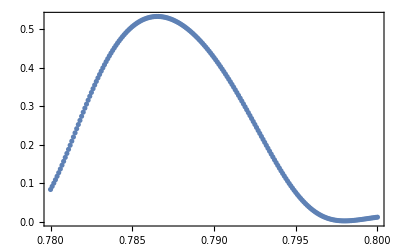
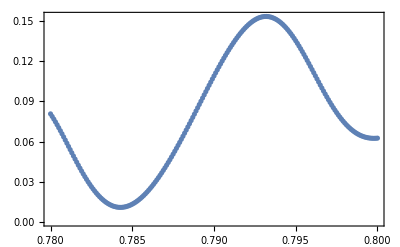
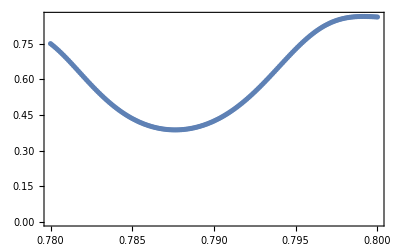
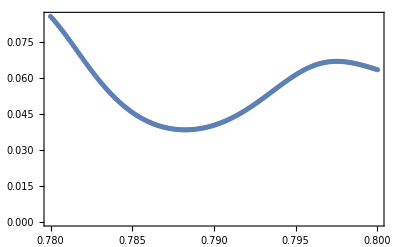

```mathematica
Module[{ii,ll=lk03},Table[ListPlot[Join[Transpose[{ll[[All,1]]}],Transpose[{Abs[ll[[All,2]][[All,ii]]]^2}],2],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
lk04=Module[{k0,ip=0,im=1,k0i=SetPrecision[0.78,Infinity],k0f=SetPrecision[0.8,Infinity],dk0=1/10000,np=SetPrecision[0.99,Infinity],tt},tt=ParallelTable[{k0,ScAmplitPlane[ip,im,k0,np,0,pp]},{k0,k0i,k0f,dk0}]];
```

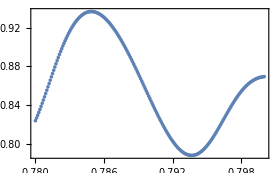
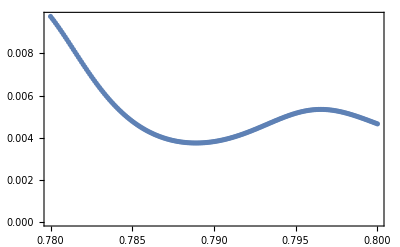
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{ii,ll=lk04},Table[ListPlot[Join[Transpose[{ll[[All,1]]}],Transpose[{Abs[ll[[All,2]][[All,ii]]]^2}],2],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
(*^^^^^^^^^^-ищем полную щель-^^^^^^^^^^^*)
```

```mathematica
(*^^^^^^^-плоские фотоны-^^^^^^^*)
```

```mathematica
(*vvvvv-закрученные фотоны-vvvvvv*)
```

```mathematica
(*нужно сначала вызвать ll=ScAmplTwistTab[ip,im,m,k00,kpp,pp], а потом ScAmplTwist[m,num,ll[[3]]] для нужного значения m; num=1-4, соответствует {rp,rm,tp,tm} для заданного значения m*)
```

```mathematica
ScAmplTwistTab[1,0,1,3,3/5,pp];//RepeatedTiming
```

{1.92,Null}

```mathematica
ll1=Module[{ip=0,im=1,m=0,k00=SetPrecision[0.61,Infinity],np=1/50,kpp},
kpp=k00 np;
ScAmplTwistTab[ip,im,m,k00,kpp,pp]];
```

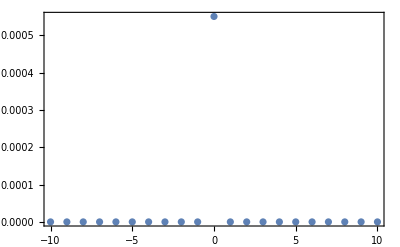
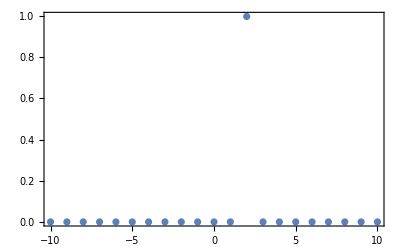
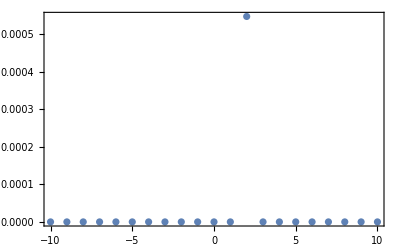
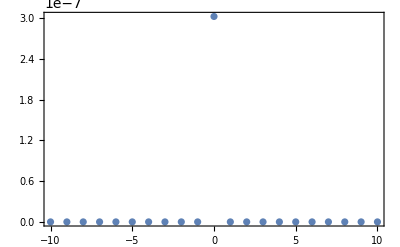

```mathematica
Module[{ll=ll1,ii,m},
Table[ListPlot[Table[{m,Abs[ScAmplTwist[m,ii,ll[[3]]]^2]},{m,-mMax,mMax}],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
ll11=Module[{ip=1,im=0,m=0,k00=SetPrecision[0.61,Infinity],np=1/50,kpp},
kpp=k00 np;
ScAmplTwistTab[ip,im,m,k00,kpp,pp]];
```

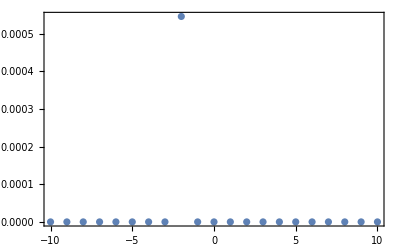
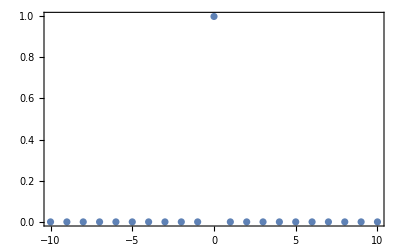
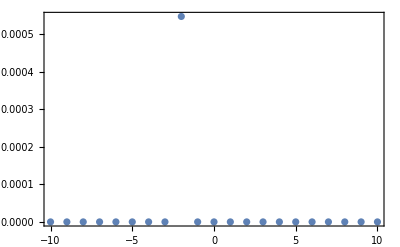
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{ll=ll11,ii,m},
Table[ListPlot[Table[{m,Abs[ScAmplTwist[m,ii,ll[[3]]]^2]},{m,-mMax,mMax}],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
ll12=Module[{ip=0,im=1,m=2,k00=SetPrecision[0.61,Infinity],np=1/50,kpp},
kpp=k00 np;
ScAmplTwistTab[ip,im,m,k00,kpp,pp]];
```

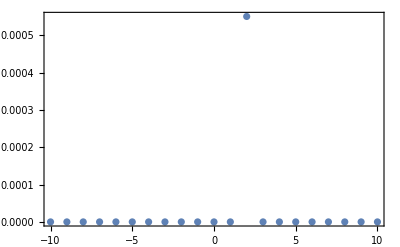
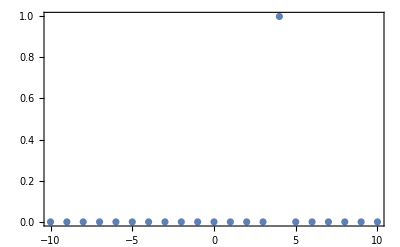
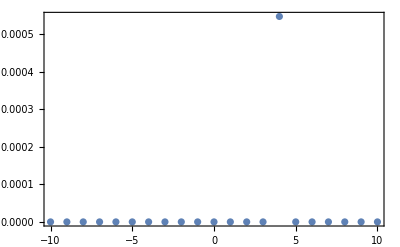
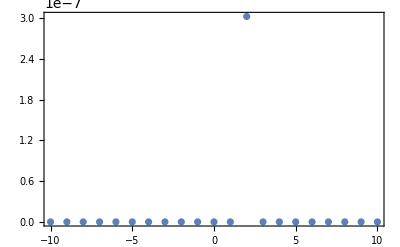

```mathematica
Module[{ll=ll12,ii,m},
Table[ListPlot[Table[{m,Abs[ScAmplTwist[m,ii,ll[[3]]]^2]},{m,-mMax,mMax}],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
ll13=Module[{ip=1,im=0,m=2,k00=SetPrecision[0.61,Infinity],np=1/50,kpp},
kpp=k00 np;
ScAmplTwistTab[ip,im,m,k00,kpp,pp]];
```

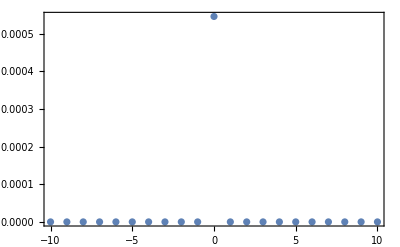
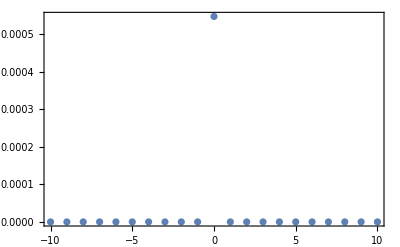
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{ll=ll13,ii,m},
Table[ListPlot[Table[{m,Abs[ScAmplTwist[m,ii,ll[[3]]]^2]},{m,-mMax,mMax}],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
(*vvvvvvv+отражение на полной щели+vvvvvvvvvv*)
```

```mathematica
ll3=Module[{ip=0,im=1,m=0,k00=SetPrecision[0.785,Infinity],np=SetPrecision[0.99,Infinity],kpp},
kpp=k00 np;
ScAmplTwistTab[ip,im,m,k00,kpp,pp]];
```

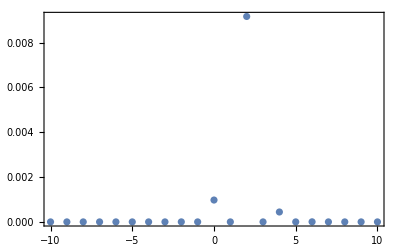
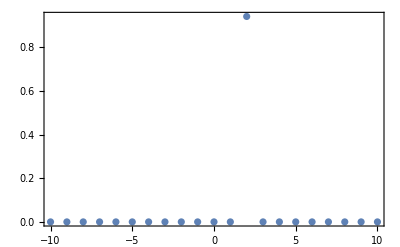
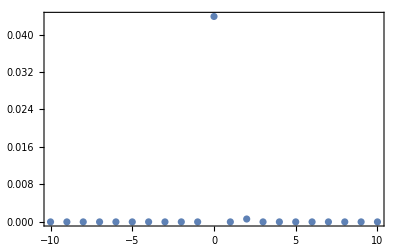
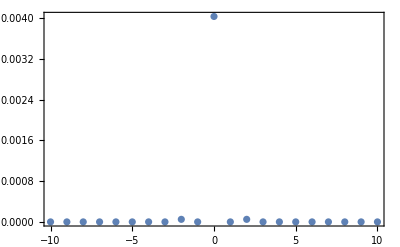

```mathematica
Module[{ll=ll3,ii,m},
Table[ListPlot[Table[{m,Abs[ScAmplTwist[m,ii,ll[[3]]]^2]},{m,-mMax,mMax}],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
ll4=Module[{ip=1,im=0,m=0,k00=SetPrecision[0.785,Infinity],np=SetPrecision[0.99,Infinity],kpp},
kpp=k00 np;
ScAmplTwistTab[ip,im,m,k00,kpp,pp]];
```

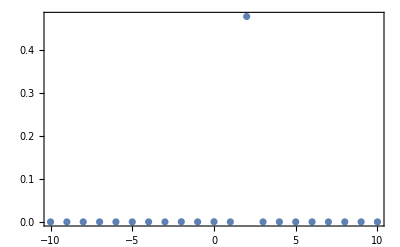
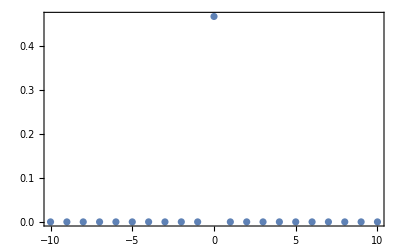
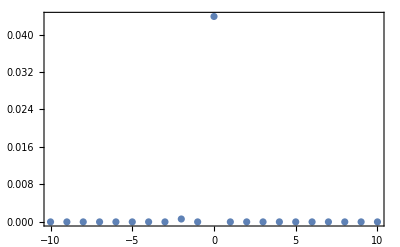
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{ll=ll4,ii,m},
Table[ListPlot[Table[{m,Abs[ScAmplTwist[m,ii,ll[[3]]]^2]},{m,-mMax,mMax}],PlotRange->Full,Frame->True],{ii,1,4}]]
```

```mathematica
(*^^^^^^^^^+отражение на полной щели+^^^^^^^^^^*)
```

```mathematica
(*^^^^^-закрученные фотоны-^^^^^^*)
```

```mathematica
(*^^^^^^-примеры-^^^^^^*)
```